# GHZ STATES - Simulation

## N = 6, Depth=14

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=6;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

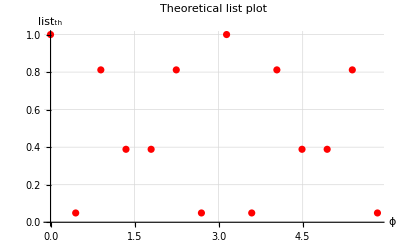

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

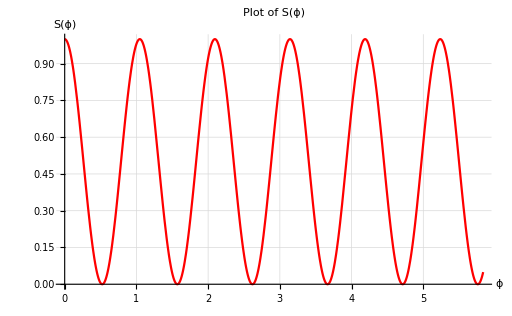

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

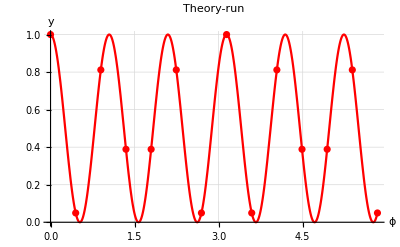

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

SIMULATION

```mathematica
data1={1.0,0.05078125,0.81103515625,0.3846435546875,0.3818359375,0.8150634765625,0.0504150390625,1.0,0.0479736328125,0.8045654296875,0.39599609375,0.388671875,0.80908203125,0.0484619140625};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0507813,0.811035,0.384644,0.381836,0.815063,0.050415,1.,0.0479736,0.804565,0.395996,0.388672,0.809082,0.0484619}

14

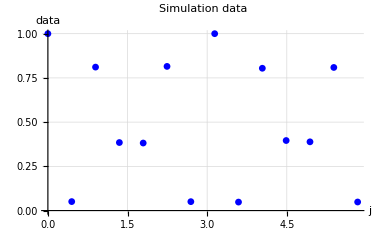

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}];
```

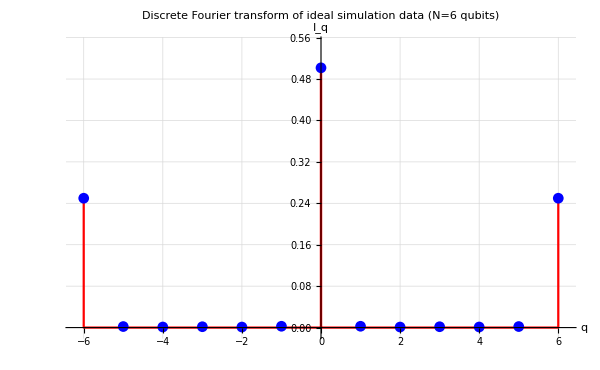

```mathematica
verticalSize=430;
orSize=600;
Fideale=Insert[Insert[Insert[Insert[Subscript[F, th],0,2],0,n+1+1],0,n+1+1+1+1],0,2n+1+1+1+1];
lideale=Insert[Insert[Insert[Insert[l,-n,2],0,n+1+1],0,n+1+1+1+1],n,2n+1+1+1+1];
FPlotideale=ListLinePlot[Thread[{lideale,Fideale}],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red}];

Show[FPlotideale,Subscript[FPlot, sim],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->20],Style["I_q",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",16,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red},ImageSize->{orSize,verticalSize}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.999538

0.999359

COMPARE

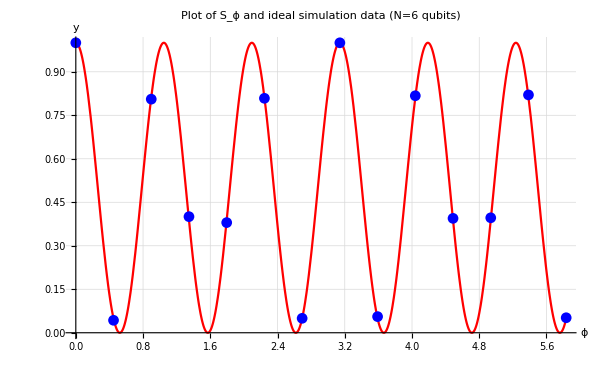

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->20],Style["y",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",18,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},ImageSize->{orSize,verticalSize}]
```

## N = 22, Depth=46

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=22;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

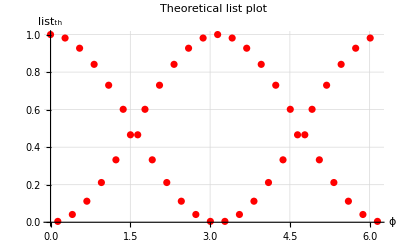

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

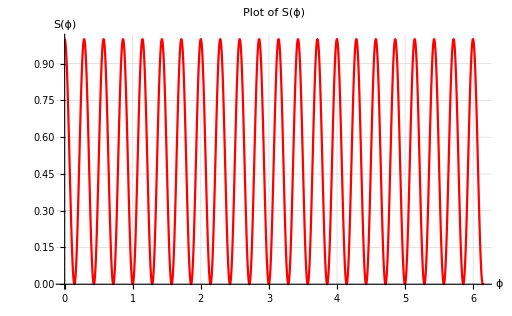

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

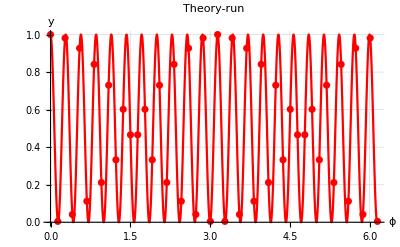

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

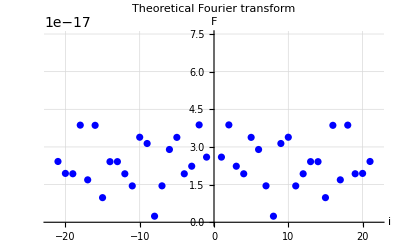

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={8.0,0.0458984375,7.8603515625,0.3427734375,7.41796875,0.8447265625,6.6943359375,1.6884765625,5.8583984375,2.6240234375,4.7666015625,3.736328125,3.720703125,4.7744140625,2.66796875,5.8837890625,1.642578125,6.734375,0.8740234375,7.466796875,0.322265625,7.865234375,0.04296875,8.0,0.04296875,7.853515625,0.298828125,7.4443359375,0.857421875,6.755859375,1.75390625,5.8544921875,2.7314453125,4.798828125,3.689453125,3.76953125,4.759765625,2.642578125,5.833984375,1.677734375,6.7822265625,0.904296875,7.4228515625,0.3583984375,7.8681640625,0.0322265625}/8;
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0057373,0.982544,0.0428467,0.927246,0.105591,0.836792,0.21106,0.7323,0.328003,0.595825,0.467041,0.465088,0.596802,0.333496,0.735474,0.205322,0.841797,0.109253,0.93335,0.0402832,0.983154,0.00537109,1.,0.00537109,0.981689,0.0373535,0.930542,0.107178,0.844482,0.219238,0.731812,0.341431,0.599854,0.461182,0.471191,0.594971,0.330322,0.729248,0.209717,0.847778,0.113037,0.927856,0.0447998,0.983521,0.00402832}

46

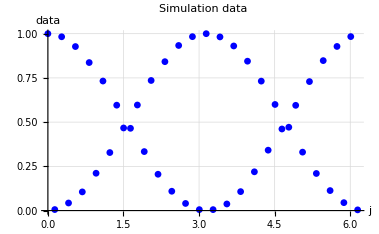

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=22 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}];
```

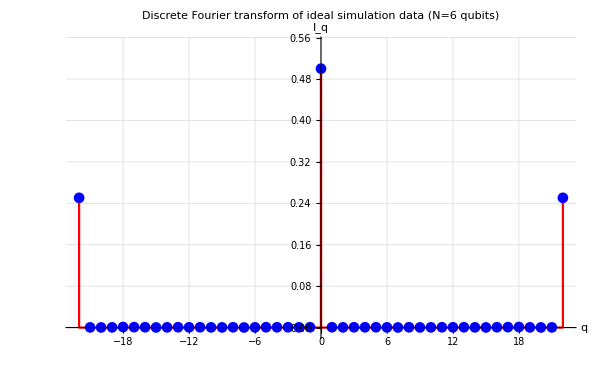

```mathematica
verticalSize=430;
orSize=600;
Fideale=Insert[Insert[Insert[Insert[Subscript[F, th],0,2],0,n+1+1],0,n+1+1+1+1],0,2n+1+1+1+1];
lideale=Insert[Insert[Insert[Insert[l,-n,2],0,n+1+1],0,n+1+1+1+1],n,2n+1+1+1+1];
FPlotideale=ListLinePlot[Thread[{lideale,Fideale}],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red}];

Show[FPlotideale,Subscript[FPlot, sim],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.3,n+0.3},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red} ,ImageSize->{orSize,verticalSize}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

1.00113

1.00058

COMPARE

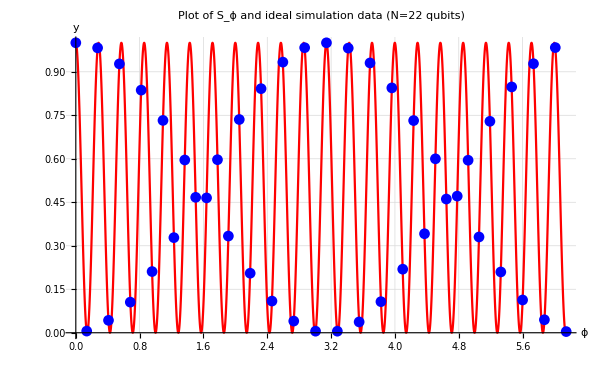

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=22 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},ImageSize->{orSize,verticalSize}]
```

## N = 24, Depth=50

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=24;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

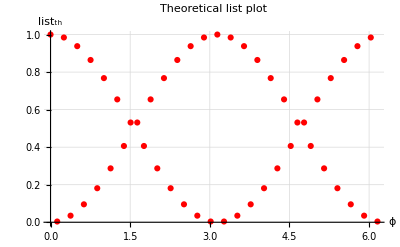

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

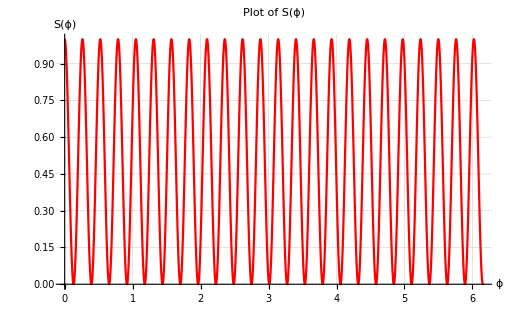

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

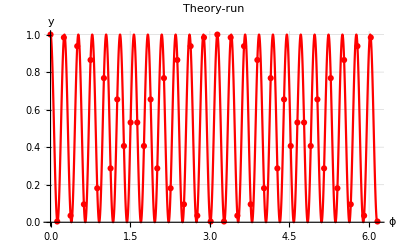

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

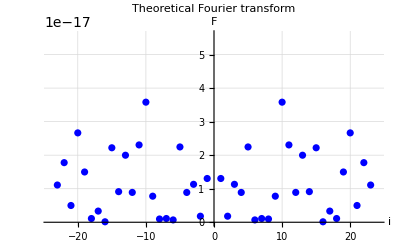

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.00390625,0.9825439453125,0.0302734375,0.9371337890625,0.096435546875,0.8712158203125,0.1864013671875,0.7681884765625,0.2821044921875,0.6534423828125,0.40087890625,0.527099609375,0.5384521484375,0.40966796875,0.6568603515625,0.29150390625,0.77294921875,0.1781005859375,0.8623046875,0.0989990234375,0.934814453125,0.0345458984375,0.9853515625,0.0037841796875,1.0,0.0042724609375,0.983642578125,0.033935546875,0.94091796875,0.093505859375,0.8623046875,0.1790771484375,0.761474609375,0.2933349609375,0.6522216796875,0.4024658203125,0.533203125,0.53369140625,0.406494140625,0.6536865234375,0.291748046875,0.7708740234375,0.17919921875,0.8641357421875,0.0911865234375,0.942138671875,0.0364990234375,0.98486328125,0.0032958984375};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.00390625,0.982544,0.0302734,0.937134,0.0964355,0.871216,0.186401,0.768188,0.282104,0.653442,0.400879,0.5271,0.538452,0.409668,0.65686,0.291504,0.772949,0.178101,0.862305,0.098999,0.934814,0.0345459,0.985352,0.00378418,1.,0.00427246,0.983643,0.0339355,0.940918,0.0935059,0.862305,0.179077,0.761475,0.293335,0.652222,0.402466,0.533203,0.533691,0.406494,0.653687,0.291748,0.770874,0.179199,0.864136,0.0911865,0.942139,0.036499,0.984863,0.0032959}

50

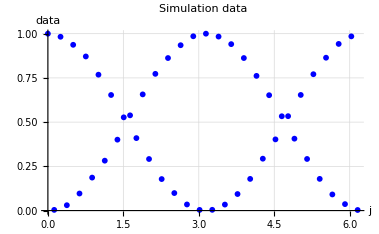

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

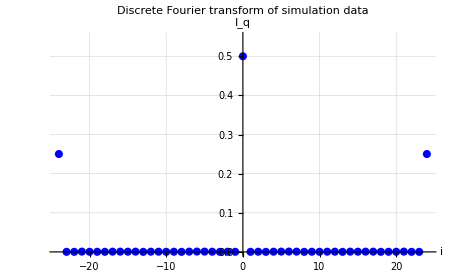

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

1.00035

1.00023

COMPARE

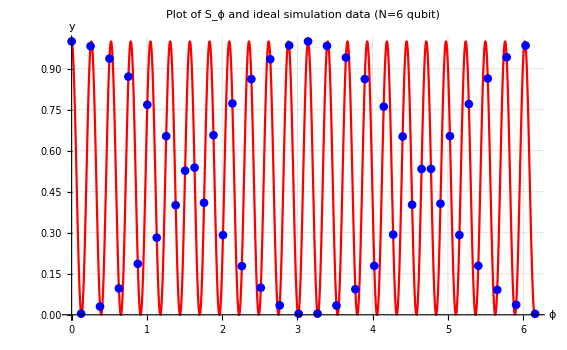

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->
{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕ and ideal simulation data (N=6 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```